#### Definitions

full, dumb recursion

```mathematica
IterateDumb[rho_, den_, lnu_,nmax_,lmax_]:=
Flatten[Table[
rho[X[[1,1]]+1,
(* concatenate the indices from the previous covariant with the new ones*)
(* k is the angular index from the nu-1 covariant-> X[[1,3,2]]*)
Join[X[[1,2]],{n,l,X[[1,3,2]] }],
{(-1)^(l+X[[1,3,2]]+lam)*X[[1,3,1]],lam}]
-> 
Table[
Sum[ ClebschGordan[{l,m},{X[[1,3,2]],mu-m},{lam,mu}] *den[{n,l,(-m)}] * 
(*pick the right "q" component of the nu-1 covariant*)
X[[2,mu-m+X[[1,3,2]]+1]],
{m,Max[-l,mu-X[[1,3,2]]],Min[l,mu+X[[1,3,2]]]}],
{mu,-lam,lam}],
{lam,0,lmax},{X, lnu},{l,Abs[lam-X[[1,3,2]]],Min[lam+X[[1,3,2]],lmax]},{n,1,nmax}] ]
```

```mathematica
IterateSortedLambda[rho_, den_, lnu_,nmax_,lmax_,lam_]:=
Flatten[Table[
rho[X[[1,1]]+1,
(* concatenate the indices from the previous covariant with the new ones*)
(* k is the angular index from the nu-1 covariant-> X[[1,3,2]]*)
Join[X[[1,2]],{n,l,X[[1,3,2]] }],
{(-1)^(l+X[[1,3,2]]+lam)*X[[1,3,1]],lam}]-> Table[
Sum[ 
ClebschGordan[{l,m},{X[[1,3,2]],mu-m},{lam,mu}] *den[{n,l,(-m)}] * 
(*pick the right "q" component of the nu-1 covariant*)
X[[2,mu-m+X[[1,3,2]]+1]],
{m,Max[-l,mu-X[[1,3,2]]],Min[l,mu+X[[1,3,2]]]}],
{mu,-lam,lam}],
{X, lnu},
{l,Max[X[[1,2,-2]],Abs[lam-X[[1,3,2]]]](*sorts the l because we start at l_nu-1*),Min[lam+X[[1,3,2]],lmax]},{n,If[l>X[[1,2,-2]],1,X[[1,2,-3]]] (*if l equals the last l, sort the n, so we start from the last n*),nmax}
] ]
```

```mathematica
IterateSorted[rho_, den_, lnu_,nmax_,lmax_]:=Flatten[Table[IterateSortedLambda[rho,den,lnu,nmax,lmax,lam],{lam,0,lmax}]]
```

```mathematica
PrecomputeCG[lmax_]:=
Table[
ClebschGordan[{l1,m},{l2,mu-m},{lam,mu}],
{l1,0,lmax},{l2,0,lmax},{lam,Abs[l1-l2],Min[l1+l2,lmax]},{mu,-lam,lam},{m,Max[-l1,mu-l2],Min[l1,mu+l2]}
]
CGFetch[cglist_,l1_,l2_,lam_,mu_]:=cglist[[1+l1,1+l2,1+lam-Abs[l1-l2],1+mu+lam]]
```

```mathematica
IterateSortedLambdaCG[rho_, den_, lnu_,nmax_,lmax_,cglist_, lam_]:= (*uses precomputed CGs -- much faster*)
Flatten[Table[
rho[X[[1,1]]+1,
(* concatenate the indices from the previous covariant with the new ones*)
(* k is the angular index from the nu-1 covariant-> X[[1,3,2]]*)
Join[X[[1,2]],{n,l,X[[1,3,2]] }],
{(-1)^(l+X[[1,3,2]]+lam)*X[[1,3,1]],lam}]-> Table[
CGFetch[cglist,l,X[[1,3,2]],lam,mu].Table[ den[{n,l,(-m)}] * 
(*pick the right "q" component of the nu-1 covariant*)
X[[2,mu-m+X[[1,3,2]]+1]],
{m,Max[-l,mu-X[[1,3,2]]],Min[l,mu+X[[1,3,2]]]}],
{mu,-lam,lam}] ,
{X, lnu},
{l,Max[X[[1,2,-2]],Abs[lam-X[[1,3,2]]]](*sorts the l because we start at l_nu-1*),Min[lam+X[[1,3,2]],lmax]},{n,If[l>X[[1,2,-2]],1,X[[1,2,-3]]] (*if l equals the last l, sort the n, so we start from the last n*),nmax}] ]
IterateSortedCG[rho_, den_, lnu_,nmax_,lmax_]:=Flatten[Table[IterateSortedLambdaCG[rho,den,lnu,nmax,lmax,lam],{lam,0,lmax}]]
```

gram-schmidt orthogonalization of a sparse matrix without turning into a full matrix!

```mathematica
Module[{res,sp,pnz},
SparseGS[mat_, thresh_:1*^-20]:=
(res=mat;
sp=Total/@(res^2);
pnz=Flatten[Position[sp,x_/;x>thresh]]; (*skips zero rows*)
If[Length[pnz]>1,
res[[pnz[[1]]]]/=Sqrt[sp[[pnz[[1]]]] ];
Do[
sp=res[[pnz[[;;(i-1)]]]].res[[pnz[[i]]]];
(*If[sp^2>thresh,res[[i]]-=sp*res[[j]]] (*has already been normalized...*),*)
res[[pnz[[i]]]]-=sp.res[[pnz[[;;(i-1)]]]];
sp=Total[res[[pnz[[i]]]]^2];
If[sp^2>thresh,res[[pnz[[i]]]]/=Sqrt[sp]];
,
{i,2,Length[pnz]}];
];
res
)
]
```

given a polynomial and a set of variables, extracts a list of coefficients into the form
{n1, n2, n3 .... nvar} -> coeff
which corresponds to the monomial var1^n1 var2^n2 ....

```mathematica
Module[{coarr,sarules,apos},
SparseCoefficientList[poly_,var_]:=(
t4+=Timing[coarr=CoefficientArrays[poly, var];][[1]];
sarules=Flatten[
{If[coarr[[1]]=!=0,
ConstantArray[0,Length[var]]->coarr[[1]],
{}
],
Table[
apos=ConstantArray[0,Length[var]];
Do[apos[[j]]+=1,{j,ar[[1]]}];
apos->ar[[2]],{i,2,Length[coarr]},{ar,Drop[ArrayRules[coarr[[i]]],-1 ]}]
}];
sarules
)]
```

consolidates list of coefficients into a list of unique coefficients and a matrix of coefficient values

```mathematica
Module[{ucoef, ncoef, npoly,ukey,upoly,mat},
ConsolidateSparseList[cpoly_]:=(
npoly=Length[cpoly];
(*pattern matching is much faster if coefficients are just enumerated, rather than listed in the explicit form above*)
ucoef=Union[Flatten[cpoly[[;;,;;,1]],1] ]; ncoef=Length[ucoef]; ukey=AssociationThread[ucoef,Range[ncoef]];
upoly = cpoly/.ukey;
mat ={};
 Do[
If[Length[upoly[[i]] ]>0,
mat=Join[mat,({i,#[[1]]}->#[[2]])&/@ Transpose[{upoly[[i,;;,1]],upoly[[i,;;,2]]} ]]
],{i,1,Length[upoly]}];
{ucoef,If[Length[mat]>0,SparseArray[mat],{}]}
)]
```

picks a block of {σ,λ} equivariants

```mathematica
ExtractSL[invlist_,sl_]:=Cases[invlist,Verbatim[Rule][_[_,_,sl],_],{1}];
```

cleans a list of invariants finding those that are linearly independent (and nonzero, of course)

```mathematica
Module[{slsel,sinv,cl,mat,omat,mono,zl,nzl,nonz,zero,slm,upper,other,nlist,llist,nllist},
CleanAll[invlist_,ldens_,lmax_]:=(
{t1,t2,t3,t4,t5}={0,0,0,0,0};zl={}; nzl={};
Do[
slsel =ExtractSL[invlist,{s,l}];
slsel = CleanList[slsel,ldens,lmax,l];
nzl=Join[nzl,slsel[[1]]];
zl=Join[zl,slsel[[2]]];
,
{s,{-1,1}},{l,0,lmax}];(*iterates over parity and l separately*)
{nzl,zl}
);
CleanList[invlist_,ldens_,lmax_,l_]:=(
(* entries with all {n,l} different are definitely independent *)
nlist=invlist[[;;,1,2,1;;;;3]];
llist=invlist[[;;,1,2,2;;;;3]];
nllist=Table[{llist[[i,j]],nlist[[i,j]] },{i,1,Length[llist]},{j,1,Length[llist[[i]] ]}];
upper=Flatten[Position[nllist,x_List/;DuplicateFreeQ[x],{1}] ];
other=Complement[Range[Length[invlist]],upper];
(* make decisions based on the first m=0 *)
t1+=Timing[sinv =SparseCoefficientList[#,ldens]&/@invlist[[other,2,1+l]];][[1]];
Print["Sparse coefficients size ", Length[sinv]];
t2+=Timing[{cl,mat}= ConsolidateSparseList[sinv];][[1]];
Print["Monomer size ", Length[cl]];
t3+=Timing[omat = SparseGS[1.*mat];][[1]];
(*mm=mat;*)
(*Print[mat, omat];*)
(* all the vectors that are nonzero after orthogonalization are linearly independent*)
nonz =Flatten[ Position[Table[omat[[i]].omat[[i]],{i,1,Length[omat]}],x_/;(x>1.*^-20),{1}]];
{Join[invlist[[upper]],invlist[[other[[nonz]] ]] ], 
invlist[[other[[Complement[Range[Length[other]],nonz] ]] ]] }
)
]
```

covariants are stored as a list of the form
rho[nu, feature_indices, {sigma,lambda}] -> { vector_of_2lambda+1 covariants}

```mathematica
Module[{lden,lrho,cglist,lz,lnz,crho,lrhoz,time1, time2},
GenerateEquivariants[nmax_,lmax_,numax_,rho_:ρ,den_:ρ0,bailouttime_:0]:=
(
lden = Flatten[Table[den[{n,l,m}],{n,1,nmax},{l,0,lmax},{m,-l,l}]];
crho = Flatten[Table[rho[1,{n, lam, lam},{1,lam}] -> Table[den[{n, lam, (-mu)}],{mu,-lam,lam}],{n,1,nmax}, {lam,0,lmax} ]];
time1=Timing[cglist=PrecomputeCG[lmax];][[1]];
Print["Precomputed CG: ",time1];
lrhoz={}; lrho=crho;
Do[
time1=Timing[crho=IterateSortedCG[rho, den, crho,nmax,lmax,cglist];][[1]];
Print["Iteration done. Generated: ", Length[crho], " new equivariants"];
time2=Timing[{lnz,lz} = CleanAll[crho,lden,lmax];][[1]];
Print["Computed ",nu, "; ", Length[lnz],"/",Length[lz], " INDEP/DEP components; Timing: ",{time1,time2} ,{t1,t2,t3,t4}];
lrho=Join[lrho,lnz]; lrhoz=Join[lrhoz,lz]; crho=lnz;
If[bailouttime>0 && (time1+time2)>bailouttime, Print["Bailing out of calculation, getting too slow!"];Return[{lrho,lrhoz}]]
,{nu,2,numax}];
{lrho,lrhoz}
)]
```

```mathematica
Module[{lden,lrho,cglist,lz,lnz,crho,nrho,nrhol,nrhoz,lrhoz,time1, time2,mxtime,tottime},
GenerateEquivariants[nmax_,lmax_,numax_,rho_:ρ,den_:ρ0,bailouttime_:0]:=
(
lden = Flatten[Table[den[{n,l,m}],{n,1,nmax},{l,0,lmax},{m,-l,l}]];
crho = Flatten[Table[rho[1,{n, lam, lam},{1,lam}] -> Table[den[{n, lam, (-mu)}],{mu,-lam,lam}],{n,1,nmax}, {lam,0,lmax} ]];
time1=Timing[cglist=PrecomputeCG[lmax];][[1]];
Print["Precomputed CG: ",time1];
lrhoz={}; lrho=crho;
Do[
nrho={};nrhoz={};mxtime=0;tottime=0;{t1,t2,t3,t4,t5}={0,0,0,0,0};
Do[(*iterate one lambda at a time*)
time1=Timing[nrhol=IterateSortedLambdaCG[rho, den, crho,nmax,lmax,cglist,lam];][[1]];
time2=0;
Do[
time2+=Timing[{lnz,lz} = CleanList[ ExtractSL[nrhol,{s,lam}],lden,lmax,lam];][[1]];
nrho=Join[nrho,lnz]; nrhoz=Join[nrhoz,lz];,
{s,{-1,1}}];
mxtime=Max[mxtime,time1+time2];
tottime+=time1+time2;
,
{lam,0,lmax}];
lrho=Join[lrho,nrho];lrhoz=Join[lrhoz,nrhoz];
Print["Computed ",nu, "; ", Length[nrho],"/",Length[nrhoz], " INDEP/DEP components; Timing: ",tottime ,{t1,t2,t3,t4}];
crho=nrho;
If[nu<numax&&bailouttime>0 && mxtime>bailouttime, Print["Bailing out of calculation, getting too slow!"];
(*one extra effort to get another round of invariants*)
nrhol=.;nrho=.;
Print["Invariant iteration ", Length[crho]];
nrhol=ExtractSL[IterateSortedLambdaCG[rho, den, crho,nmax,lmax,cglist,0],{1,0}];
Print["Invariant size ", Length[nrhol]]; crho=.;
{lnz,lz} = CleanList[nrhol,lden,lmax,0];
lrho=Join[lrho,lnz];lrhoz=Join[lrhoz,lz]; 
Return[{lrho,lrhoz}]];
,{nu,2,numax}];
{lrho,lrhoz}
)]
```

## Generate all covariants up to given order, given lmax, nmax, numax

```mathematica
nmax=4
lmax=4
numax=3
```

4

4

3

```mathematica
Timing[cglist=PrecomputeCG[lmax];]
```

{0.901994,Null}

density coefficients

```mathematica
lden = Flatten[Table[den[{n,l,m}],{n,1,nmax},{l,0,lmax},{m,-l,l}]];
```

```mathematica
{lnz,lz}=GenerateEquivariants[nmax, lmax, numax,rho,den,10];
```

Precomputed CG: 1.11574

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 20

Monomer size 60

Sparse coefficients size 16

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 16

Monomer size 52

Sparse coefficients size 12

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 12

Monomer size 48

Computed 2; 530/28 INDEP/DEP components; Timing: 0.295731{0.012855,0.004391,0.006227,0.008406}

Sparse coefficients size 76

Monomer size 924

Sparse coefficients size 192

Monomer size 2136

Sparse coefficients size 242

Monomer size 1668

Sparse coefficients size 300

Monomer size 1560

Sparse coefficients size 290

Monomer size 1340

Sparse coefficients size 402

Monomer size 2232

Sparse coefficients size 344

Monomer size 1732

Sparse coefficients size 364

Monomer size 1560

Sparse coefficients size 268

Monomer size 1310

Sparse coefficients size 418

Monomer size 2216

Computed 3; 10660/716 INDEP/DEP components; Timing: 30.2482{8.7885,5.10804,6.28091,7.3937}

```mathematica
lnz
```

{rho[1,{1,0,0},{1,0}]→{den[{1,0,0}]},11208,rho[3,{4,3,3,4,3,3,4,4,4},{1,4}]→{√(14/143) (-√(5/11) den[{4,3,2}]^2+2 √(3/11) den[{4,3,1}] den[{4,3,3}]) den[{4,4,0}]-√(35/143) (-(2 den[{4,3,1}] den[{4,3,2}])/(√11)+3 √(2/11) den[{4,3,0}] den[{4,3,3}]) den[{4,4,1}]+3 √(5/143) (1) den[{4,4,2}]-√(35/143) (-√(30/77) den[{4,3,0}] den[{4,3,1}]+(8 den[{1}] den[{4,3,2}])/(√77)+2 √(15/77) den[{4,3,-2}] den[{4,3,3}]) den[{4,4,3}]+√(14/143) (-3 √(2/77) den[{4,3,0}]^2+√(2/77) den[{4,3,-1}] den[{4,3,1}]+√(14/11) den[{4,3,-2}] den[{4,3,2}]+3 √(2/77) den[{4,3,-3}] den[{4,3,3}]) den[{4,4,4}],7,1}}
 |  |  |  |

count of non-zero coefficients matching [nu, _, {sigma, lambda}]

```mathematica
Length[Cases[lnz[[;;,1]],_[2,_,{1,0}]]]
```

50

```mathematica
Cases[lz[[;;,1]],_[3,_,{1,0}]]
```

```mathematica
Length[Cases[lz[[;;,1]],_[2,_,{1,1}]]]
```

0

```mathematica
Export[
NotebookDirectory[]<>"indep-nmax-lmax.dat",
Prepend[lnz[[;;,1]]/.(_[nu_,ll_,{s_,l_}] -> Join[{nu, s, l}, ll]),{"# nu sigma lambda n1 l1 k1 [n2 l2 k2 .....]"}]
]
Export[
NotebookDirectory[]<>"zerodep-nmax-lmax.dat",
Prepend[lz[[;;,1]]/.(_[nu_,ll_,{s_,l_}] -> Join[{nu, s, l}, ll]),{"# nu sigma lambda n1 l1 k1 [n2 l2 k2 .....]"}]
]
```

/home/michele/lavoro/code/nice/enumerate/indep-nmax-lmax.dat

/home/michele/lavoro/code/nice/enumerate/zerodep-nmax-lmax.dat

scans a grid of nmax and lmax, printing out the lists of in/cov ariants

```mathematica
Do[
Print["COMPUTING NONZERO EQUIVARIANTS FOR nmax=", n, " lmax= ",l];
{lnz,lz}=GenerateEquivariants[n,l,8,rho,den,6];
Export[
NotebookDirectory[]<>"indep-"<>ToString[n]<>"-"<>ToString[l]<>".dat",
Prepend[lnz[[;;,1]]/.(_[nu_,ll_,{sig_,lam_}] -> Join[{nu, sig, lam}, ll]),{"# nu sigma lambda n1 l1 k1 [n2 l2 k2 .....]"}],"Table", "FieldSeparators"->" "];
Export[
NotebookDirectory[]<>"zerodep-"<>ToString[n]<>"-"<>ToString[l]<>".dat",
Prepend[lz[[;;,1]]/.(_[nu_,ll_,{sig_,lam_}] -> Join[{nu, sig, lam}, ll]),{"# nu sigma lambda n1 l1 k1 [n2 l2 k2 .....]"}],"Table", "FieldSeparators"->" "];,
{n,3,3},{l,8,8}]
```

COMPUTING NONZERO EQUIVARIANTS FOR nmax=3 lmax= 8

Precomputed CG: 9.45975

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 27

Monomer size 135

Sparse coefficients size 24

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 24

Monomer size 129

Sparse coefficients size 21

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 21

Monomer size 126

Sparse coefficients size 18

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 18

Monomer size 117

Sparse coefficients size 15

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 0

Monomer size 0

Sparse coefficients size 15

Monomer size 105

Computed 2; 1674/78 INDEP/DEP components; Timing: 3.31768{0.062111,0.053047,0.035256,0.04666}

Sparse coefficients size 156

Monomer size 5661

Sparse coefficients size 315

Monomer size 10986

Sparse coefficients size 516

Monomer size 10026

Sparse coefficients size 624

Monomer size 9510

Sparse coefficients size 738

Monomer size 8919

Sparse coefficients size 894

Monomer size 11577

Sparse coefficients size 933

Monomer size 10419

Sparse coefficients size 996

Monomer size 9699

Sparse coefficients size 984

Monomer size 9048

Sparse coefficients size 1155

Monomer size 11757

Sparse coefficients size 1098

Monomer size 10536

Sparse coefficients size 1125

Monomer size 9723

Sparse coefficients size 1029

Monomer size 8994

Sparse coefficients size 1236

Monomer size 11688

Sparse coefficients size 1095

Monomer size 10488

Sparse coefficients size 1086

Monomer size 9606

Sparse coefficients size 906

Monomer size 8787

Sparse coefficients size 1143

Monomer size 11559

Computed 3; 80388/4044 INDEP/DEP components; Timing: 385.082{64.4262,42.5818,176.715,57.1928}

Bailing out of calculation, getting too slow!

Invariant iteration 80388

Invariant size 37320

Sparse coefficients size 12864

```mathematica
Length[Cases[lz[[;;,1]],_[6,_,{1,0}]]]
Length[Cases[lnz[[;;,1]],_[6,_,{1,0}]]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

```mathematica
mm
```

mm

```mathematica
t=Sum[1,{l1,1,ln},{l2,l1,ln},{l3,l2,ln},{l4,l3,ln}]
```

1/24 (6 ln+11 ln^2+6 ln^3+ln^4)

```mathematica
FullSimplify[t]
```

1/24 ln (1+ln) (2+ln) (3+ln)

```mathematica
FullSimplify[(ln+4-1)!/(ln-1)!]/4!
```

1/24 ln (1+ln) (2+ln) (3+ln)

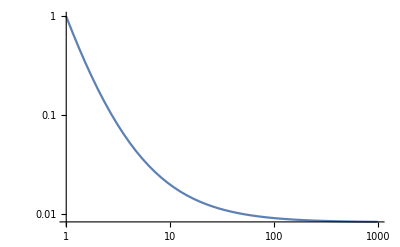

```mathematica
LogLogPlot[Evaluate[((ln+nu-1)!/(nu!(ln-1)!)/ln^nu)/.nu->5],{ln,1,1000}]
```

```mathematica
ldens = Flatten[Table[ρ0[{n,l,m}],{n,1,nmax},{l,0,lmax},{m,-l,l}]];
```

```mathematica
t1=Timing[sinv =Simplify[SparseCoefficientList[#,ldens]&/@ExtractSL[lnz,{1,2}][[;;,2,1+0]]];][[1]];
```

$Aborted

```mathematica
t2=Timing[{cl,mat}= ConsolidateSparseList[sinv];][[1]];
```

```mathematica
Dimensions[mat]
MatrixRank[mat]
```

{153,1009}

153

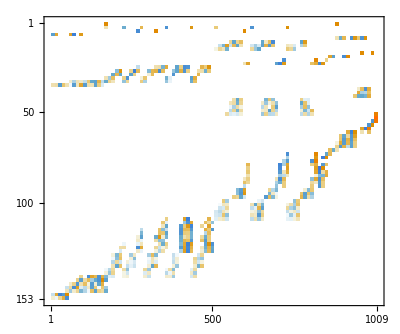

```mathematica
mat//MatrixPlot
```

```mathematica
Cases[lnz[[;;,1]],_[_,_,{1,0}]]
```

{rho[1,{1,0,0},{1,0}],rho[1,{2,0,0},{1,0}],rho[1,{3,0,0},{1,0}],rho[2,{1,0,0,2,0,0},{1,0}],rho[2,{1,0,0,3,0,0},{1,0}],rho[2,{1,1,1,2,1,1},{1,0}],rho[2,{1,1,1,3,1,1},{1,0}],rho[2,{1,2,2,2,2,2},{1,0}],2615,rho[4,{3,3,3,3,3,3,1,4,4,1,4,4},{1,0}],rho[4,{3,3,3,3,3,3,1,4,4,2,4,4},{1,0}],rho[4,{3,3,3,3,3,3,1,4,4,3,4,4},{1,0}],rho[4,{3,3,3,3,3,3,2,4,4,2,4,4},{1,0}],rho[4,{3,3,3,3,3,3,2,4,4,3,4,4},{1,0}],rho[4,{3,3,3,3,3,3,3,4,4,3,4,4},{1,0}],rho[4,{3,4,4,3,4,4,3,4,0,3,4,4},{1,0}],rho[4,{3,4,4,3,4,4,3,4,2,3,4,4},{1,0}]}
 |  |  |  |

```mathematica
Cases[lz[[;;,1]],_[2,_,{1,0}]]
```

{ρ[2,{1,0,0,1,0,0},{1,0}],ρ[2,{1,1,1,1,1,1},{1,0}],ρ[2,{1,2,2,1,2,2},{1,0}],ρ[2,{1,3,3,1,3,3},{1,0}],ρ[2,{1,4,4,1,4,4},{1,0}],ρ[2,{2,0,0,2,0,0},{1,0}],ρ[2,{2,1,1,2,1,1},{1,0}],ρ[2,{2,2,2,2,2,2},{1,0}],ρ[2,{2,3,3,2,3,3},{1,0}],ρ[2,{2,4,4,2,4,4},{1,0}],ρ[2,{3,0,0,3,0,0},{1,0}],ρ[2,{3,1,1,3,1,1},{1,0}],ρ[2,{3,2,2,3,2,2},{1,0}],ρ[2,{3,3,3,3,3,3},{1,0}],ρ[2,{3,4,4,3,4,4},{1,0}],ρ[2,{4,0,0,4,0,0},{1,0}],ρ[2,{4,1,1,4,1,1},{1,0}],ρ[2,{4,2,2,4,2,2},{1,0}],ρ[2,{4,3,3,4,3,3},{1,0}],ρ[2,{4,4,4,4,4,4},{1,0}],ρ[2,{5,0,0,5,0,0},{1,0}],ρ[2,{5,1,1,5,1,1},{1,0}],ρ[2,{5,2,2,5,2,2},{1,0}],ρ[2,{5,3,3,5,3,3},{1,0}],ρ[2,{5,4,4,5,4,4},{1,0}]}

```mathematica
ρ[2,{1,0,0,1,0,0},{1,0}]/.lz
```

{ρ0[{1,0,0}]^2}

```mathematica
mm
```

SparseArray[<10336>, {847, 4164}]

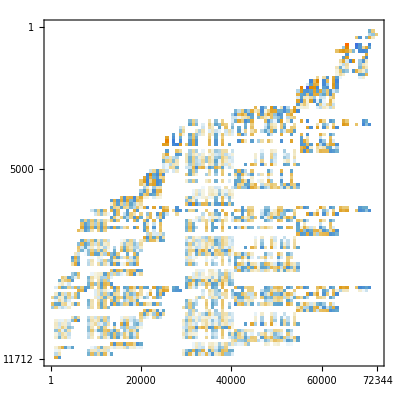

```mathematica
mm//MatrixPlot
```

```mathematica
smm
```

SparseArray[…]

```mathematica
Count[Total/@(mmm^2),x_/;x>1.*^-20]
Count[Total/@(mm^2),x_/;x>1.*^-20]
Count[Total/@(smm^2),x_/;x>1.*^-20]
```

388

418

388

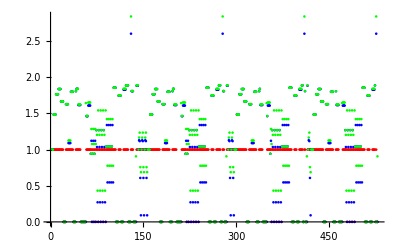

```mathematica
ListPlot[
{Transpose[{Range[Length[mm]],Total/@(mmm^2)}],
Transpose[{Range[Length[mm]],Total/@(smm^2)}],
Transpose[{Range[Length[mm]],Total/@(mm^2)}]
},PlotStyle->{Red,Blue,Green}]
```

```mathematica
530"/"28" "10660"/"1404
```

computes number of *clearly* independent equivariants of a given order (all l different but sorted)

```mathematica
NDistinct[nmax_,lmax_,nu_]:=
(
```

```mathematica
Cases[lnz[[;;,1]],_[2,_,{-1,1}]]
```

{}

```mathematica
lz
```

{}

```mathematica
Cases[lnz[[;;,1]],ρ[2,___]]
```

{ρ[2,{1,1,1,1,2,1},{-1,2}],ρ[2,{1,2,2,1,3,2},{-1,2}],ρ[2,{1,3,3,1,4,3},{-1,2}],ρ[2,{1,1,1,1,3,1},{-1,3}],ρ[2,{1,2,2,1,4,2},{-1,3}],ρ[2,{1,1,1,1,4,1},{-1,4}],ρ[2,{1,2,2,1,3,2},{-1,4}],ρ[2,{1,3,3,1,4,3},{-1,4}],ρ[2,{1,0,0,1,0,0},{1,0}],ρ[2,{1,1,1,1,1,1},{1,0}],ρ[2,{1,2,2,1,2,2},{1,0}],ρ[2,{1,3,3,1,3,3},{1,0}],ρ[2,{1,4,4,1,4,4},{1,0}],ρ[2,{1,0,0,1,1,0},{1,1}],ρ[2,{1,1,1,1,2,1},{1,1}],ρ[2,{1,2,2,1,3,2},{1,1}],ρ[2,{1,3,3,1,4,3},{1,1}],ρ[2,{1,0,0,1,2,0},{1,2}],ρ[2,{1,1,1,1,3,1},{1,2}],ρ[2,{1,2,2,1,4,2},{1,2}],ρ[2,{1,1,1,1,1,1},{1,2}],ρ[2,{1,2,2,1,2,2},{1,2}],ρ[2,{1,3,3,1,3,3},{1,2}],ρ[2,{1,4,4,1,4,4},{1,2}],ρ[2,{1,0,0,1,3,0},{1,3}],ρ[2,{1,1,1,1,2,1},{1,3}],ρ[2,{1,1,1,1,4,1},{1,3}],ρ[2,{1,2,2,1,3,2},{1,3}],ρ[2,{1,3,3,1,4,3},{1,3}],ρ[2,{1,0,0,1,4,0},{1,4}],ρ[2,{1,1,1,1,3,1},{1,4}],ρ[2,{1,2,2,1,4,2},{1,4}],ρ[2,{1,2,2,1,2,2},{1,4}],ρ[2,{1,3,3,1,3,3},{1,4}],ρ[2,{1,4,4,1,4,4},{1,4}]}

```mathematica
lnz
```

{ρ[1,{1,0,0},{1,0}]→{ρ0[{1,0,0}]},ρ[1,{1,1,1},{1,1}]→{ρ0[{1,1,1}],ρ0[{1,1,0}],ρ0[{1,1,-1}]},1531,ρ[3,{2,4,4,2,4,4,2,4,0},{1,4}]→{ρ0[{2,4,4}] (1/3 ρ0[{2,4,0}]^2-2/3 ρ0[{2,4,-1}] ρ0[{2,4,1}]+2/3 ρ0[{2,4,-2}] ρ0[{2,4,2}]-2/3 ρ0[{2,4,-3}] ρ0[{2,4,3}]+2/3 ρ0[{2,4,-4}] ρ0[{2,4,4}]),7,ρ0[{2,4,-4}] (1)},ρ[3,{2,4,4,2,4,4,2,4,2},{1,4}]→{1}}
 |  |  |  |

#### nu=1 covariants

```mathematica
nie[1] = Flatten[Table[ rho[1,{n, lam, lam},{1,lam}] -> Table[den[{n, lam, (-mu)}],{mu,-lam,lam}],{n,1,nmax}, {lam,0,lmax} ]];
```

#### nu=2, sorted iteration

```mathematica
Timing[snie[2]=IterateSortedCG[rho, den, nie[1],nmax,lmax,cglist];]
```

{0.069984,Null}

we need to iterate over

```mathematica
Length[snie[2]]
```

106

```mathematica
Timing[{snie[2],zl2}=CleanList[snie[2],lden,lmax];]
```

{0.016767,Null}

#### nu=3, sorted iteration (starting from minimal nu=2 case)

```mathematica
Timing[snie[3]=IterateSortedCG[rho, den, snie[2],nmax,lmax,cglist];]
```

{0.529236,Null}

```mathematica
Length[snie[3]]
```

1107

```mathematica
Timing[{snie[3],zl3} = CleanList[snie[3],lden,lmax];]
```

{20.503,Null}

```mathematica
Length[snie[3]]
```

927

#### nu=4, sorted iteration

```mathematica
Timing[snie[4]=IterateSortedCG[rho, den, snie[3],nmax,lmax,cglist];]
```

{12.0094,Null}

```mathematica
Length[snie[4]]
```

9301

```mathematica
Timing[{snie[4],zl4}=CleanList[snie[4],lden,lmax];]
```

{1891.71,Null}

```mathematica
Length[snie[4]]
```

7647

```mathematica
Simplify[snie[4][[1,2]]]
```

{1/(2 √5)(-den[{1,1,1}] (den[{1,2,1}] den[{2,1,-1}]^2-√3 den[{1,2,0}] den[{2,1,-1}] den[{2,1,0}]+den[{1,2,-1}] den[{2,1,0}]^2+den[{1,2,-1}] den[{2,1,-1}] den[{2,1,1}]-√2 den[{1,2,-2}] den[{2,1,0}] den[{2,1,1}])+den[{1,1,0}] (√2 den[{1,2,2}] den[{2,1,-1}]^2-den[{1,2,1}] den[{2,1,-1}] den[{2,1,0}]+den[{2,1,1}] (den[{1,2,-1}] den[{2,1,0}]-√2 den[{1,2,-2}] den[{2,1,1}]))+den[{1,1,-1}] (-√2 den[{1,2,2}] den[{2,1,-1}] den[{2,1,0}]+den[{2,1,1}] (-√3 den[{1,2,0}] den[{2,1,0}]+den[{1,2,-1}] den[{2,1,1}])+den[{1,2,1}] (den[{2,1,0}]^2+den[{2,1,-1}] den[{2,1,1}])))}